## Auf der Suche nach A^-2 für GUP-“inspired” in N dim

### Die Metrik

```mathematica
γ[n_,z_] = Gamma[n,0,z];
g00[n_,z_] = 1-(2 M  γ[2+n,z])/z^(1+n)
```

1-2 M z^(-1-n) Gamma[2+n,0,z]

```mathematica
Manipulate[
Plot[  1-(2 M  γ[2+n,z])/z^(1+n), {z,0,4}, PlotRange->{-1,1}],
{{M,1.5},0,10},
{n,0,6,1}]
```

### Werte für r_0 und M_*

```mathematica
miniToSol[res_] := res /. {y_,{_ -> x_}} -> {x,y} (* for FindMinimum -> Coordinate  *)
rootToSol[res_] := res  /. {_ -> x_} -> x (* for first FindRoot -> value *)
```

```mathematica
maxN = 7;
```

```mathematica
r0s = First@Transpose@Table[miniToSol@FindMinimum[
Re@g00[n,r]/.M-> 3, {r,1}
 ],{n,0,maxN}];
(* fi3d extremal Mass values *)
Ms = Table[rootToSol@FindRoot[Re@g00[n,r]/.r-> r0s⟦n+1⟧, {M,3}] ,{n,0,maxN}];
Grid[{
{"n"}~Join~Range[0,maxN],
{"r_0"}~Join~r0s,
{"M_*"}~Join~Ms
}, Frame-> All]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum :: lstol will be suppressed during this calculation.

n | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
r_0 | 1.79328 | 1.45123 | 1.31433 | 1.24065 | 1.19472 | 1.1634 | 1.1407 | 1.1235
M_* | 1.67546 | 2.9412 | 4.24808 | 5.57428 | 6.9109 | 8.25373 | 9.60055 | 10.9501

### Metrik-Plot zum Export

```mathematica
(* Prepare Export and metric units *)
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
(* Epic Epilog-Labels coming here, modified for the current problem:
   Featuring scaling and correct Inset (no rectangle nonrotated box).
 ASSUMING data be a list of X as variable, ideal for g00s. *)
ClearAll[EpiLabels]
EpiLabels[xpoint_, data_, labels_,axisratio_:1]:= 
With[{xpoints=If[Head@xpoint===List, xpoint, xpoint&/@ labels]}, (* erlaube Liste von xpoints *)
Inset[Rotate[Text[labels[[#]],Background -> White],
ArcTan@Re@N[(D[data⟦#⟧,X]/.{X-> xpoints⟦#⟧}) ] / axisratio] ,
{xpoints⟦#⟧, 0 +( data/.X-> xpoints⟦#⟧)⟦#⟧}
]& /@ Range@Length@data] (* 1: any value to introspect list*)

point[color_, coord_,size_:0.37] := Inset[
Graphics@{Opacity[0.9], color, Disk[]},
(* {x,y}, {xOrig,yOrig}, scaling --> see Inset doku *)
coord, {0,0}, size
]
Ω[d_] := (2 Pi^((d+1)/2))/Gamma[(d+1)/2] (* Kugeloberflaeche *)
```

```mathematica
Block[{a=3,b=a+4},b]
```

7

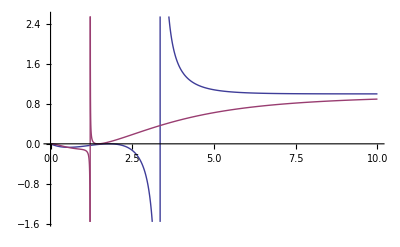

```mathematica
Plot[Evaluate@{
Block[{n=0},g00[n,r]/(1-(2M  8π)/((n+2)Ω[n+2])1/r^(1+n)) /. M-> Ms⟦n+1⟧],
Block[{n=1},g00[n,r]/(1-M/2 1/r^(1+n)) /. M-> Ms⟦n+1⟧]
},{r,0,10}]
```

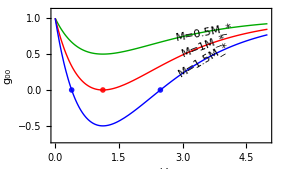

```mathematica
(* @Re@: Cut off small imaginary parts *)
fig =Module[{n=7,chosenM},
factors={0.5,1,1.5};
chosenM=factors*Ms⟦n+1⟧;
pointSize=0.15;
labels = "M="<>ToString@#<> "M_*"&/@factors ;
labelsSMM = "STM, "<>#&/@labels;
g00A[n_,z_] = 1-(2 M   γ[2+n,z])/z^(1+n);
Plot[Evaluate@Re@Flatten@Table[
{g00[n,r](*, SMM*)}/.{M-> M},{M,chosenM}], {r,0,5},
PlotRangePadding->0,
PlotStyle->{Darker@Green, Red, Blue},
Frame-> True,
FrameLabel->{"r / L","g_00"},
PlotRange-> {-0.7,1.1},
Epilog-> {
EpiLabels[3.5,g00A[n,r]/.{M-> #,r-> X}&/@ chosenM,labels,6/10],
point[Red,{r0s⟦1+n⟧,0},pointSize],
point[Blue, {rootToSol@FindRoot[Re@g00[n,r]/. M-> Last@chosenM,{r,1}],0},pointSize],
point[Blue, {rootToSol@FindRoot[Re@g00[n,r]/. M-> Last@chosenM,{r,2}],0},pointSize]
},
ImageSize -> 10cm,
AspectRatio-> 0.6
(* wird in Latex gemacht: *)
(*lotLabel-> "Metric component g_00 of modified GUP in n=2 LXDs"]*)
]]
```

```mathematica
Export["../figures/g00_n7.pdf", Show@fig]
```

../figures/g00_n7.pdf

### Werte für A^-2

```mathematica
(* Liste der A[p] *)
Avals = Table[(-1)^(N-3)(I ((N-3)!))/(2p Sqrt[β])(1/(1+I Sqrt[β]p)^(N-2)-1/(1-I Sqrt[β]p)^(N-2))/.N-> n// FullSimplify ,{n,3,maxN+3}];
(* Liste der f[p] *)
fs = ((1/# - 1  // FullSimplify)&/@ Avals);
```

```mathematica
Grid[Transpose@{
{"n"}~Join~Range[0,maxN],
{"A_n"}~Join~Avals,
{"test1"}~Join~fs,
{"test2"}~Join~Table[(n-3)!, {n,3,maxN+3}]
}, Frame-> All]
```

n | A_n | test1 | test2
0 | 1/(1+p^2 β) | p^2 β | 1
1 | -2/((1+p^2 β)^2) | -1-1/2 (1+p^2 β)^2 | 1
2 | (6-2 p^2 β)/((1+p^2 β)^3) | -1+((1+p^2 β)^3)/(6-2 p^2 β) | 2
3 | (24 (-1+p^2 β))/((1+p^2 β)^4) | -1+((1+p^2 β)^4)/(24 (-1+p^2 β)) | 6
4 | (24 (5+p^2 β (-10+p^2 β)))/((1+p^2 β)^5) | -1+((1+p^2 β)^5)/(24 (5+p^2 β (-10+p^2 β))) | 24
5 | -(240 (-3+p^2 β) (-1+3 p^2 β))/((1+p^2 β)^6) | -1-((1+p^2 β)^6)/(240 (-3+p^2 β) (-1+3 p^2 β)) | 120
6 | -(720 (-7+p^2 β (35+p^2 β (-21+p^2 β))))/((1+p^2 β)^7) | -1-((1+p^2 β)^7)/(720 (-7+p^2 β (35+p^2 β (-21+p^2 β)))) | 720
7 | (40320 (-1+p^2 β) (1+p^2 β (-6+p^2 β)))/((1+p^2 β)^8) | -1+((1+p^2 β)^8)/(40320 (-1+7 p^2 β-7 p^4 β^2+p^6 β^3)) | 5040

```mathematica
Series[-1-1/2 (1+p^2 β)^2,{p,0,3}]
```

-3/2-β p^2+O[p]^4

```mathematica
Table[Series[(-1)^(N-3)(I ((N-3)!))/(2p Sqrt[β])(1/(1+I Sqrt[β]p)^(N-2)-1/(1-I Sqrt[β]p)^(N-2))/.N-> n,{p,0,2}],{n,3,8}]
```

{1-β p^2+O[p]^3,-2+4 β p^2+O[p]^3,6-20 β p^2+O[p]^3,-24+120 β p^2+O[p]^3,120-840 β p^2+O[p]^3,-720+6720 β p^2+O[p]^3}

### Plots der GUP-Kurven

```mathematica
(* GUP-Kurve *)
xB[f_,p_] = (1+f[p])/(2p);
size=7.5cm;
```

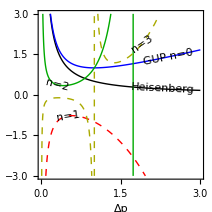

```mathematica
funks = {1/(2p)}~Join~Table[xB[fs⟦1+n⟧/.{p-> #, β-> 1}&,p],{n,0,3}];
fig=Plot[
Evaluate@funks,{p,0,3},
PlotRange->  {-3,3},
PlotStyle-> {{Thick,Black},{Thick,Blue},{Dashed,Red},Darker@Green, {Dashed,Darker@Yellow}},
Epilog->{
EpiLabels[{2.3, 2.4, 0.5, 0.3,1.9},
funks/.p-> X,{"Heisenberg", "GUP n=0", "n=1", "n=2", "n=3"},2],
},
AspectRatio->1,
PlotRangePadding->None,
Frame-> True,
FrameLabel-> {"Δp","Δx"},
ImageSize-> size
]
```

```mathematica
Export["../figures/gup-mod-mod.pdf", fig]
```

../figures/gup-mod-mod.pdf

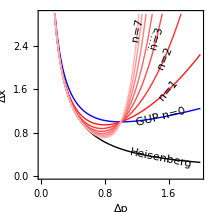

```mathematica
funks={1/(2p)}~Join~Table[xB[#^(2+n)&,p],{n,0,7}];
fig=Plot[Evaluate@funks,{p,0,2},
PlotRange-> {0,3},
AspectRatio->1,
PlotRangePadding->None,
PlotStyle->{{Thick,Black},{Thick,Blue}}~Join~(Lighter[Red, 0.8*Rescale[#,{0,8}]]&/@Range[8]),
Epilog->{
EpiLabels[{1.5, 1.5, 1.6, 1.55, 1.45, 1.34, 1.29, 1.20, 1.21},
funks/.p-> X,{"Heisenberg","GUP n=0","n=1","n=2","n=3","......","","","n=7"},1.1],
},
Frame-> True,
FrameLabel-> {"Δp","Δx"},
ImageSize-> size
]
```

```mathematica
Export["../figures/gup-mod.pdf", fig]
```

../figures/gup-mod.pdf